# Chapter 8 - Problem 1

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
e = 1.60217 * 10^-19;
nano = 1 * 10^-9;
```

The length of the well is 1 nm

```mathematica
L = 1*nano;
```

#### This is configuration C from his notes:

(Chapter 8 - Page 6) We have here the infinite potential well with an electric field present. THe infinite potential well (width L) requires that:
ϕ(z = 0) = ϕ(z = L) = 0

The Solution of the Schrodinger equation is a linear combination of Ai and Bi.

First let’s build the matrix with the boundary conditions above, then we can find the determinant of that matrix, finally given above to find when this determinant is equal to zero.

We will be breaking the equation into parts with substitutions to make things a little easier to write.

First let’s see the transfer matrix when the electric field strength = 5 V/nm

```mathematica
F = 0.5 * 1/nano; (*5 volts per nano meter*)
a = ((2*m)/ℏ^2 * e *F)^(1/3);
b =(-en * e)/(e*F);
```

```mathematica
m11 = AiryAi[a *b];
m12 = AiryBi[a*b];
m21 = AiryAi[a*(b-L)];
m22 = AiryBi[a * (b-L)];
transfer = {{m11,m12},{m21,m22}};
```

```mathematica
det = m11 * m22 - m12 * m21
```

AiryAi[-4.7175 en] AiryBi[2.35875×10^9 (-1/1000000000-2.×10^-9 en)]-AiryAi[2.35875×10^9 (-1/1000000000-2.×10^-9 en)] AiryBi[-4.7175 en]

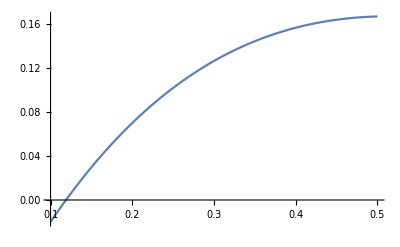

```mathematica
Plot[det,{en,0.1,0.5}]
```

So then our ground state energy when the electric field is 0.5 V/nm is:

```mathematica
FindRoot[det == 0,{en, 0.1}]
```

{en→0.118857}

Cool so that worked!

Now we just need to do it for a table of values

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
e = 1.60217 * 10^-19;
nano = 1 * 10^-9;
voltspernano = 1/nano;
L = 1*nano;
a = ((2*m)/ℏ^2 * e *F)^(1/3);
b =(-en * e)/(e*F); 
m11 = AiryAi[a *b];
m12 = AiryBi[a*b];
m21 = AiryAi[a*(b-L)];
m22 = AiryBi[a * (b-L)];
det = m11 * m22 - m21* m12
```

-AiryAi[2.97184×10^6 (-1/1000000000-(1. en)/F) F^(1/3)] AiryBi[-(2.97184×10^6 en)/F^(2/3)]+AiryAi[-(2.97184×10^6 en)/F^(2/3)] AiryBi[2.97184×10^6 (-1/1000000000-(1. en)/F) F^(1/3)]

Now the determinant is a function of both the energy and the electric field

```mathematica
Table[FindRoot[det==0,{en,0.13}],{F,0.1*voltspernano, 0.5*voltspernano, 0.01*voltspernano}];
groundenergy = en/.%
```

{0.325744,0.320683,0.315617,0.310545,0.305468,0.300384,0.295295,0.2902,0.285099,0.279993,0.274881,0.269763,0.264639,0.259509,0.254374,0.249233,0.244087,0.238935,0.233776,0.228613,0.223443,0.218268,0.213087,0.2079,0.202708,0.19751,0.192306,0.187097,0.181882,0.176661,0.171434,0.166202,0.160964,0.15572,0.150471,0.145216,0.139956,0.134689,0.129418,0.12414,0.118857}

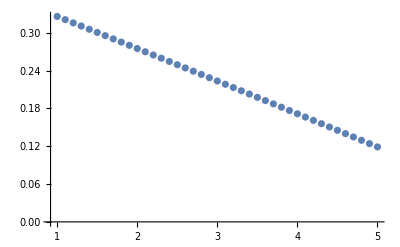

```mathematica
F = Table[F,{F,0.1*voltspernano, 0.5*voltspernano, 0.01*voltspernano}]; (* values of F in table form*)
ListPlot[Table[{F[[i]], groundenergy[[i]]}, {i,1,Length[F]}]]
```

#### What we see:

We can see that there is an inverse linear relationship between the ground state energy and the electric field strength. As the electric field strength increases, the ground state energy of the particle begins to fall.